5

0.1

9.81

-0.5+m0

9.81 (-0.5+m0)

0.1 v

{{a→-(1. (9.81 (-0.5+m0)-0.1 v))/(-0.5+m0)}}

1

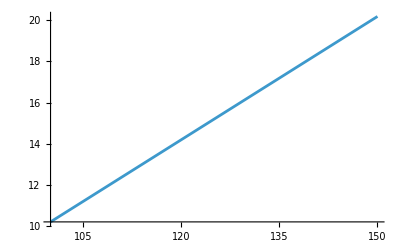

1.5

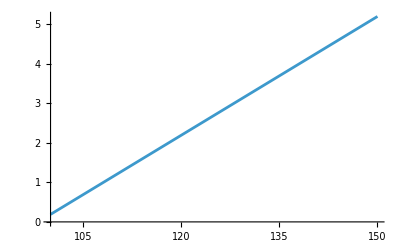

```mathematica
ClearAll["Global`*"]
t=5
mi=0.1(*kg/s*)
g=9.81
(**)
m[t_]=m0-mi*t
F[t_]=m[t]*g
Fc=v*mi
rown=Solve[Fc-F[t]==m[t]*a,a]
(*m0=1*)
m0=1
Plot[a/.rown[[1]],{v,100,150}]
(*m0=1.5*)
m0=1.5
Plot[a/.rown[[1]],{v,100,150}]
```